# Discover the Higgs

Total: /

In this project we simulate the Higgs discovery search recorded by CMS in
https://arxiv.org/pdf/1207.7235.pdf
In particular, we focus on the Higgs →ZZ^*→4l channel described in section 5.2. 
Please read the introduction from this paper. This semester’s class should have prepared you to understand much of what is written. From the introduction you can answer the following questions:
Question 1: Is the Higgs discovery claim from one individual search channel or a combination of several channels? (2/2)
Answer: A combination of several channels.
Question 2: Which two channels were most sensitive to the Higgs? (2/2)
Answer: H -> γγ and H -> ZZ
Question 3: What two center of mass energy runs are being combined in this analysis? (2/2)
Answer: Gamma and Z bosons

Before we get to section 5.2 we need some information from Table 1 on page 5. 
Question 4: What integrated luminosity was recorded for the H→ZZ decay mode at 7 TeV and 8 TeV? (2/2)
Answer: 5.1 and 5.3

Note that the units for luminosity given here are in inverse femtobarns rather than inverse piccobarns. 
Question 5: How many pb^-1 are in one fb^-1? (2/2)
Answer: 10^-3
For this study we will not take into account the subtely of running at two different energies.  Instead we pretend that we have 10.4 fb^-1 of integrated luminosity at 8 TeV. Let’s record this now for use later. Because we are recording the integrated luminosity in inverse femtobarns we will need to make sure all cross sections are also expressed in femtobarns.
Directive 1: Record the integrated luminosity in inverse femtobarns. (2/2)

```mathematica
Lumifb=10.4;
```

Now, let’s move on to section 5.2.
Question 6: What requirements do electrons need to pass to make it into the data set? (2/2)
Answer: pT > 7 GeV and |η| < 2.5.
Question 7: What requirements do muon need to pass to make it into the data set? (2/2)
Answer:  pT > 5 GeV and |η| < 2.4.
Question 8: What do you think it means that electrons and muon must be isolated? (2/2)
Answer: It means that they cannot be a mixture of electrons with other particles. They need to be on their own so that we can get data from them.

Regarding ZZ^* reconstruction on page 12.
Question 9: Give an example of “same flavor, oppositely charged leptons.” (2/2)
Answer: An electron and a positron
Ranges are given for what this search considers to be an on-shell Z boson and an off-shell Z boson. We need to know the Z mass to evaluate this. Using wikipedia or the PDG, look up the Z mass.
Question 10:  What is the mass of the Z boson in GeV? (2/2)
Answer: 90 GeV
Fig. 4 gives the background and signal predicted as well as the actual data.
Question 11: What gives rise to the big peak in the background at invariant mass of about 90 GeV? (2/2)
Answer: The five kinematics angles and the invarient masses of the two lepton pairs

Final paragraph of section 5.2 on page 14 gives the results of the search. 
Question 12: For what range of invariant mass do they find a significant excess of events over the background expectation? (2/2)
Answer: 120 < m_H < 130 GEV
Question 13: What was the expected and actual significance (in σ) of this excess? (2/2)
Answer: 3.2 (actual) and 3.8 (expected)

## Possibly Useful Functions (some new)

These are simply the functions that you likely made in the previous project. They are all given here in case you want to use them. They may or may not be necessary in what follows. A few new ones have been added here to ensure that all the following code runs.

```mathematica
ClearMemory:=Module[{},
Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];
];(*This is just to try and ensure memory stays somewhat in control.*)
eventInfo={_,_,_,_,_,_};
decayedOrIn = {_,-1,_,_,_,_,_,_,_,_,_,_,_}  | {_,2,_,_,_,_,_,_,_,_,_,_,_};
SetOut[ event_ ]  := (DeleteCases[event,decayedOrIn,2]);
ReadLHE[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
(*Throw away header info at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{_String,___}| eventInfo,2]
);
ReadEvents[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadLHE[testp]; ]; 
(*convert raw data into readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info*)
ClearMemory;
{eventListp, eventListOutLp}
];
FindParticles[event_,pidlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[pidlist],j++,
If[event[[i]][[1]] == pidlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];

GetParticles[event_,pidlist_]:=event[[FindParticles[event, pidlist]]];
PIDu= 2;
PIDubar = -2;
PIDd = 1;
PIDdbar = -1;
PIDs = 3;
PIDsbar = -3;
PIDc = 4;
PIDcbar = -4;
PIDb = 5;
PIDbbar = -5;
PIDt = 6;
PIDtbar = -6;
PIDeminus = 11;
PIDeplus = -11;
PIDnue=12;
PIDnuebar = -12;
PIDmuminus = 13;
PIDmuplus =-13;
PIDnumu = 14;
PIDnumubar = -14;
PIDtauminus = 15;
PIDtauplus = -15;
PIDnutau = 16;
PIDnutaubar = -16;
PIDgluon = 21;
PIDphoton = 22;
PIDZ = 23;
PIDWplus = 24;
PIDWminus = -24;
PIDh = 25;

PIDLeptonList={11,-11,13,-13};

particle[2] ="u";
particle[-2] ="ū";

particle[1] ="d";
particle[-1] ="d̄";

particle[3] ="s";
particle[-3] ="s̄";

particle[4] ="c";
particle[-4] ="c̄";

particle[5] ="b";
particle[-5] ="b̄";

particle[6] ="t";
particle[-6] ="t̄";

particle[11] ="e^-";
particle[-11] ="e^+";

particle[12] ="ν_e";
particle[-12] ="ν_e^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="ν_μ";
particle[-14] ="ν_μ^c";


particle[15] ="τ^-";
particle[-15]="τ^+";

particle[16] ="ν_τ";
particle[-16] ="ν_τ^c";

particle[21] ="gluon";
particle[22] = "γ";
particle[23] = "Z";
particle[24] ="W^+";
particle[-24] = "W^-";
particle[25] = "h";

finout[-1] = "in";
finout[1] = "out";
finout[2]  = "decayed";

EventPrint[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,cτ,hel}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcCos[pz/(√(px^2 + py^2+ pz^2))];
phifn[px_,py_]:=Which[
 py > 0, 
ArcTan[px,py]
,
 py < 0, 
2π + ArcTan[px,py]

];(* This function is defined such that ϕ∈[0,2π]*)

phiOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= phifn[px,py];
theta[event_] := Map[thetaOf,event,{1}]//Flatten;
phi[event_] := Map[phiOf,event,{1}]//Flatten;
rapOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=1/2 Log[(e+pz)/(e-pz)];
etaOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=-Log[Tan[1/2 ArcCos[pz/(√(px^2 + py^2+ pz^2))]]];
rap[event_] := Map[rapOf,event,{1}]//Flatten;
eta[event_] := Map[etaOf,event,{1}]//Flatten;
ptOf[{_,_,_,_,_,_,px_,py_,___}]:=√(px^2+py^2);
enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=En;
pT[event_]  :=Map[ptOf,event,{1}]//Flatten;
en[event_]:=Map[enOf,event,{1}]//Flatten;
AbsMin[list_]:=Sort[list,Abs[#1]<Abs[#2]&]⟦1⟧;
DeltaPhi[{part1_,part2_}]:=AbsMin[{
(phiOf[part1]-phiOf[part2])
,
(2 π - (phiOf[part1]-phiOf[part2]))
,
(2 π + (phiOf[part1]-phiOf[part2]))
}];
DeltaR[{part1_,part2_}]:=√((etaOf[part1] - etaOf[part2])^2+DeltaPhi[{part1,part2}]^2);
FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}] := {En, px, py,pz };
ThreeVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,___}] := { px, py,pz };
FourLength[{En_,px_,py_,pz_}] := Sqrt[En^2 - px^2 - py^2-pz^2];
InvMass[particles_]:= FourLength[ Sum[FourVectorFrom[particles[[i]]],{i,1,Length[particles]}]];
PoissonError[nobs_,CL_]:={ If[nobs ==  0, 0, InverseCDF[PoissonDistribution[nobs],1-CL]],
If[nobs==0,0,InverseCDF[PoissonDistribution[nobs],CL]]}//N

(*Default is 1-σ error*)
PoissonError[nobs_]:=PoissonError[nobs, Erf[1/Sqrt[2]]]-nobs;
```

## Background

To simulate the signal and background we are going to use the MadGraph model “heft”
This model includes effective vertices between the Higgs and gluons or photons. This is essential for the gluon fusion Higgs production cross section and we will use the same model to simulate the background for consistency.

In MadGraph type
MG5_aMC>import model heft
to load this model

We want to look at the  four lepton final state. As with the Z discovery, this is taken to imply either electrons or muons, not taus. 
So, we generate the background with
MG5_aMC>generate p p > l+ l- l+ l- /h
where the /h ensure that no Higgs interactions are included
Output the process to something like proc_heft_pp_4lep_noH

For the simulation of events we are going to set the center of mass energy to 8 TeV
# Collider type and energy                                           *
# lpp: 0=No PDF, 1=proton, -1=antiproton, 2=photon from proton,      *
#                3=photon from electron, 4=photon from muon          *
#*********************************************************************
     1        = lpp1    ! beam 1 type 
     1        = lpp2    ! beam 2 type
     4000.0     = ebeam1  ! beam 1 total energy in GeV
     4000.0     = ebeam2  ! beam 2 total energy in GeV
 Note that the collider type is proton-proton
 We need to allow pT cuts below the trigger levels of 5 and 7 GeV. So we take a 1 GeV generator cut
 #*********************************************************************
# Minimum and maximum pt’s (for max, -1 means no cut)                *
#*********************************************************************
 1.0  = ptl       ! minimum pt for the charged leptons 
 -1.0  = ptlmax    ! maximum pt for the charged leptons
 Similarly, we allow for η up to 2.6
 #*********************************************************************
# Maximum and minimum absolute rapidity (for max, -1 means no cut)   *
#*********************************************************************
 2.6  = etal    ! max rap for the charged leptons 
 0.0  = etalmin ! main rap for the charged leptons
We also are focusing on a particular possible mass range for the Higgs. Consider Fig. 4 in the CMS search. They only consider the total invariant mass of the leptons from about 70 GeV to 180 GeV. We make this cut on our events as well.
 #*********************************************************************
 # Minimum and maximum invariant mass for all letpons                 *
 #*********************************************************************
 70.0   = mmnl    ! min invariant mass for all letpons (l+- and vl) 
 180.0  = mmnlmax ! max invariant mass for all letpons (l+- and vl)

Very important!!
For some reason I have not figured out yet, the newer Phase-Space Optimization strategy completely fails for this process. When I tried to generate events it took almost an hour to run and only returned 81 events, instead of 10,000.
So, make the change
# Phase-Space Optimization strategy (basic options)
#*********************************************************************
   0  = nhel          ! using helicities importance sampling or not.
                             ! 0: sum over helicity, 1: importance sampling
   1  = sde_strategy  ! default integration strategy (hep-ph/2021.xxxxx)
                             ! 1 is old strategy (using amp square)
     ! 2 is new strategy (using only the denominator)
To use the old strategy, set sde_strategy=1, not 2.

Once these changes to the run card have been saved, proceed to generate the events, record the cross section, and load the events into this notebook. Note that this took more time to generate than our previous projects. Make sure you have the time and compute battery to make it through. If your computer has multiple cores you can engage more of them to reduce the time.
Directive 2: Generate at least 10,000 background events. (10/10)

The MadGraph cross section output is given in pb not fb.
Question 14: How many femtobarns in a piccobarn? (2/2)
Answer: 10^3
Directive 3: Record the number of events you generated and the cross section in fb (4/4)

```mathematica
939.565-938.272
```

1.293

```mathematica
√(((1.3^2+0.5^2-10^-12)/(2 1.3))^2-0.5^2)
```

0.553846

```mathematica
Nevents=10000;
σbkgd=100.6;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica\513\New folder

```mathematica
{bkgdio,bkgdo}=ReadEvents["higgs_background.lhe"];
```

Time taken to read events: 3.92188

Make a histogram similar to Fig. 4 in the CMS paper. 
That is, a histogram of the invariant mass of the four leptons in the background events. Rescale the histogram by the ratio of the expected number of background events (cross section times luminosity) to the number of simulated events.
Directive 4: Make a rescaled histogram of invariant mass of the background events. (2/2)

```mathematica
InvMassListbkgd=Flatten[InvMass/@bkgdo];
```

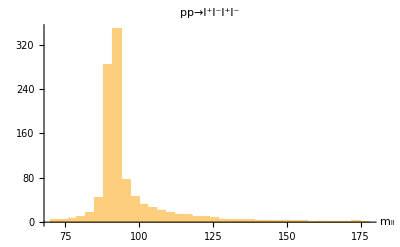

```mathematica
Histogram[InvMassListbkgd,{70,180,3},#2 (σbkgd*Lumifb)/Nevents&,PlotLabel->"pp→l^+l^-l^+l^-", AxesLabel->{"m_ll"}]
```

Question 15: How does this compare to the background histogram in Fig. 4? (2/2)
Answer: It is very similar. Their peaks occur in just about the same spot! However, their graph seems to have similar events recorded for 100 as they do 180, whereas my graph dies off at 180. Also, my y-axis has much larger values than there’s.

## Signal

Again, we are using the heft model so type make sure that you have typed
MG5_aMC>import model heft
before you create a process.

We are interested in 4 lepton final states coming from Higgs decay. This is simulated by typing
MG5_aMC>generate p p > h, h > l+ l- l+ l- 
Then output this process to something like proc_heft_pp_h_4lep

Directive 5: Make the same generator level cuts as you made for the background and generate the same number of events. (10/10)
Question 16: What cross section, in fb, do you find? (2/2)
Answer: 0.5808

Actually, we don’t want to use the MadGraph cross section. Because gluon fusion is a strong force process (so the coupling is larger) the loop effects make significant corrections to the tree-level result MadGraph uses.
However, the Higgs Cross Section Working Group has calculated many of these corrections. They are recorded conveniently here:
https://twiki.cern.ch/twiki/bin/view/LHCPhysics/CERNYellowReportPageAt8TeV
We find that for a 125 GeV Higgs the gluon fusion production cross section is 
Question 17: What is the gluon fusion cross section (in fb) at N3LO for a 125 GeV Higgs? (2/2)
Answer: 21420

Of course, most of the time the Higgs does not decay into four leptons. So we must also multiply the Higgs branching fraction into four leptons, not allowing the τ. This is found at
https://twiki.cern.ch/twiki/bin/view/LHCPhysics/CERNYellowReportPageBR
Question 18: What is the branching fraction (dimensionless) for H→4leptons, without including taus? (2/2)
Answer: 1.24e-4

The total predicted cross section is the gluon fusion cross section multiplied by this branching fraction. You should find that this is
 0.002656 pb = 2.656 fb
Question 19: How does this compare to the MadGraph cross section? (2/2)
Answer: This is about 5 times larger than the MadGraph cross section.
Directive 6: Record the signal cross section (in fb) for later use. (2/2)

```mathematica
21420*1.24*10^-4
```

2.65608

```mathematica
σsig=2.656;
```

To be clear, we can still use the MadGraph events. They do capture the correct kinematics of the events we are interested in. We just determine the predicted number of actual LHC Higgs events using a different cross section.

```mathematica
{sigio,sigo}=ReadEvents["higgs_signal.lhe"];
```

Time taken to read events: 3.54688

Directive 7: Make a rescaled invariant mass histogram of the signal events. (2/2)

```mathematica
InvMassListsig=Flatten[InvMass/@sigo];
```

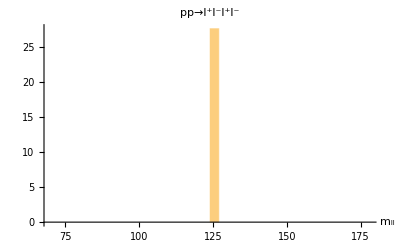

```mathematica
Histogram[InvMassListsig,{70,180,3},#2 (σsig*Lumifb)/Nevents&,PlotLabel->"pp→l^+l^-l^+l^-", AxesLabel->{"m_ll"}]
```

This looks a little too clean. 
In a real collider there is more uncertainty in the measurements. We can replicate that my “smearing” our signal events. From the abstract of 
https://arxiv.org/pdf/1306.2016.pdf
The electron energy resolution of the CMS detector at 7 TeV is at best about 2%. So, we take this MadGraph events are smear the energy of the leptons at the 2% level and adjust their momenta accordingly.

```mathematica
LepERes[E_?NumericQ]:=E 0.02;
```

```mathematica
LeptonGaussSmear[event_]:=Module[{OldleptonEvent,NewLeptonEvent,lepE,lepσ,newE,newPvec,tempEvent,i},

OldleptonEvent=GetParticles[event,PIDLeptonList];
NewLeptonEvent={};

For[i=1,i<Length[OldleptonEvent]+1,i++,
tempEvent=OldleptonEvent[[i]];

lepE=enOf[tempEvent];
lepσ=LepERes[lepE];
newE=RandomVariate[NormalDistribution[lepE,lepσ]];

newPvec=newE/lepE ThreeVectorFrom[tempEvent]; 

tempEvent[[10]]=newE;
tempEvent[[7;;9]]=newPvec;

AppendTo[NewLeptonEvent,tempEvent];
];

NewLeptonEvent

];
```

Directive 8: Smear the signal events and then remake the invariant mass histogram. (4/4)

```mathematica
smearSigo=LeptonGaussSmear/@sigo;
```

```mathematica
InvMassListSmearsig=Flatten[InvMass/@smearSigo];
```

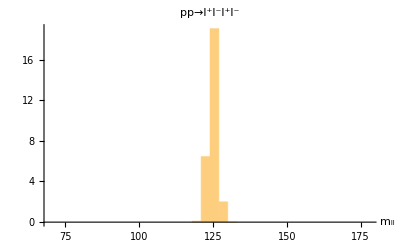

```mathematica
Histogram[InvMassListSmearsig,{70,180,3},#2 (σsig*Lumifb)/Nevents&,PlotLabel->"pp→l^+l^-l^+l^-", AxesLabel->{"m_ll"}]
```

Of course, if we are smearing the signal, we also need to smear the background to be consistent
Directive 9: Smear the background events and remake the invariant mass histogram. (4/4)

```mathematica
smearBkgdo=LeptonGaussSmear/@bkgdo;
```

```mathematica
InvMassListSmearbkgd=Flatten[InvMass/@smearBkgdo];
```

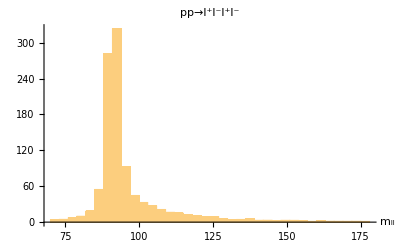

```mathematica
Histogram[InvMassListSmearbkgd,{70,180,3},#2 (σbkgd*Lumifb)/Nevents&,PlotLabel->"pp→l^+l^-l^+l^-", AxesLabel->{"m_ll"}]
```

## Cutting the Data

We now implement the CMS cuts
The lepton selection cuts are similar to those of previous projects. The cut that seeks to reconstruct the Z mass can be somewhat tricky when all four leptons are of the same flavor. We want to group opposite sign, same flavor lepton pairs together and find their invariant mass. Pairs whose invariant mass is close to the Z boson mass are likely to have been produced by the decay of an on-shell Z.
Question 20: When all four leptons are of the same flavor (e.g. two electrons and two positrons) how many unique opposite sign, same flavor two lepton invariant masses can be constructed? (2/2)
Answer: Two

We are interested in determining the invariant mass that is nearest the Z boson mass. 
Question 21: Once that pair of leptons has been identified and fixed, how many unique lepton pairs can be constructed from the remaining leptons? (2/2)
Answer: One

```mathematica
cutnames ={
"No Cuts",(*1*)
"Trigger: 4 Lepton",(*2*)
"      μμμμ",(*3*)
"      eeee",(*4*)
"      eeμμ",(*5*)
"Cut: Z mass [40,120]",(*6*)
"Cut: Z^* mass [12,120] "(*7*)
};
```

```mathematica
ApplyCuts[eventlist_]:=Module[{currentevent,trigger,mZ,electronEvent,ePlusList,eMinusList,Zfromee,muonEvent,muPlusList,muMinusList,Zfromμμ,mZlist,survivingevents,cutcounter,passcut},

mZ=91.2;

cutcounter=Table[0,{Length[cutnames]}];
survivingevents={};

(*run this each time we pass a cut*)
passcut[cutindex_]:=Module[{},
(*increment cut counter*)
cutcounter[[cutindex]]++;
];

For[i=1,i<(Length[eventlist]+1),i++,

(*Passcut after setting the variables*)
passcut[1];
trigger=0;

currentevent=eventlist[[i]];

electronEvent=GetParticles[currentevent,{PIDeminus,PIDeplus}];
(*Keep only electrons with |rapidity|≤ 2.5 and Subscript[p, T]≥ 7 GeV*)
electronEvent=Select[electronEvent,((ptOf[#]≥7)&&(Abs[etaOf[#]]<2.5))&];

muonEvent=GetParticles[currentevent,{PIDmuminus,PIDmuplus}];
(*Keep only muons with with |η|≤ 2.4 and Subscript[p, T]≥ 5 GeV*)
muonEvent=Select[muonEvent,((ptOf[#]≥5)&&(Abs[etaOf[#]]<2.4))&];

If[Length[electronEvent]+Length[muonEvent]==4,
passcut[2];

(*Four muon case*)
If[Length[muonEvent]==4,
passcut[3];

muPlusList=GetParticles[currentevent,{PIDmuplus}];
muMinusList=GetParticles[currentevent,{PIDmuminus}];

Zfromμμ={{InvMass[muPlusList[[1]],muMinusList[[1]]],InvMass[muPlusList[[1]],muMinusList[[2]]]},{InvMass[muPlusList[[2]],muMinusList[[1]]],InvMass[muPlusList[[2]],muMinusList[[2]]]}};

(*Within each possibility, put the Z which is closest to on shell first in the sublist*)
Zfromμμ=Sort[#,Abs[#1[[1]] - mZ]<Abs[#2[[1]] - mZ]&] &/@Zfromμμ;
(*Sort the sublists such that the first one has the most on shell Z*)
Zfromμμ=Sort[Zfromμμ,Abs[#1[[1,1]] - mZ]<Abs[#2[[1,1]] - mZ]&];

mZlist=Zfromμμ[[1]];

];

(* Four electron case *)
If[Length[electronEvent]==4,
passcut[4];

ePlusList=GetParticles[currentevent,{PIDeplus}];
eMinusList=GetParticles[currentevent,{PIDeminus}];

Zfromee={{InvMass[ePlusList[[1]],eMinusList[[1]]],InvMass[ePlusList[[1]],eMinusList[[2]]]},{InvMass[ePlusList[[2]],eMinusList[[1]]],InvMass[ePlusList[[2]],eMinusList[[2]]]}};

(*Within each possibility, put the Z which is closest to on shell first in the sublist*)
Zfromee=Sort[#,Abs[#1[[1]] - mZ]<Abs[#2[[1]] - mZ]&] &/@Zfromee;
(*Sort the sublists such that the first one has the most on shell Z*)
Zfromee=Sort[Zfromee,Abs[#1[[1,1]] - mZ]<Abs[#2[[1,1]] - mZ]&];

mZlist=Zfromee[[1]];

];

(* 2 muon 2 electron case *)
If[(Length[electronEvent]==2)&&(Length[muonEvent]==2),
passcut[5];

mZlist={InvMass[electronEvent],InvMass[muonEvent]};
mZlist=Sort[mZlist,Abs[#1 - mZ]<Abs[#2 - mZ]&];

];

If[40<mZlist[[1]]<120,
passcut[6];

If[12<mZlist[[2]]<120,
passcut[7];

AppendTo[survivingevents,currentevent];

];

];

];

];

{cutcounter, survivingevents}

];
```

Directive 10: Apply cuts to the smeared background (5/5)

```mathematica
{bkgdcutcounter,bkgdcutevents}=ApplyCuts[smearBkgdo];
```

Directive 11: Apply cuts to the smeared signal (5/5)

```mathematica
{sigcutcounter,sigcutevents}=ApplyCuts[smearSigo];
```

Directive 12: Make a table of the results (5/5)

```mathematica
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdcutcounter,"Background"],Prepend[sigcutcounter,"Signal"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | Background | Signal
No Cuts | 10000 | 10000
Trigger: 4 Lepton | 1325 | 4980
      μμμμ | 437 | 1394
      eeee | 245 | 1209
      eeμμ | 643 | 2377
Cut: Z mass [40,120] | 572 | 2344
Cut: Z^* mass [12,120]  | 219 | 2132

We now need to determine the physical collider level results
Directive 13: Make a table of the collider level cuts flow (5/5)

```mathematica
MCtoExpCutlist[cutlist_,NExpBeforeCuts_]:=Module[{efficiency,NExpAfterCuts,ExpError,ExpCutsWithError},
efficiency=#/cutlist[[1]]&/@ cutlist;
NExpAfterCuts=NExpBeforeCuts*#&/@efficiency;
ExpError=NExpBeforeCuts/cutlist[[1]]*PoissonError[#]&/@cutlist;
ExpCutsWithError=Table[0,{Length[cutlist]}];
For[i=1,i<(Length[ExpCutsWithError]+1),i++,
ExpCutsWithError[[i]]=Subsuperscript[ToString[NExpAfterCuts[[i]]],ToString[ExpError[[i,1]]],ToString[ExpError[[i,2]]]];
];
{ExpCutsWithError,NExpAfterCuts}
];
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgd*Lumifb)];
{sigExpCutcounterErr,sigExpCutcounter}=MCtoExpCutlist[sigcutcounter,(σsig*Lumifb)];
sigoverbkgd=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter]}];
significance=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter]}];
```

```mathematica
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr,"N_sig^Exp"],Prepend[sigoverbkgd,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 1046.24_-5.02195^4.91733 | 27.6224_-0.132588^0.129825 | 0.0264016 | 0.853976
Trigger: 4 Lepton | 138.627_-1.77861^1.77861 | 13.756_-0.0939162^0.0911539 | 0.0992301 | 1.16833
      μμμμ | 45.7207_-1.04624^1.04624 | 3.85056_-0.0497203^0.0497203 | 0.0842193 | 0.569466
      eeee | 25.6329_-0.836992^0.732368 | 3.33955_-0.0469581^0.0441958 | 0.130284 | 0.659613
      eeμμ | 67.2732_-1.25549^1.25549 | 6.56584_-0.0635315^0.0635315 | 0.0975997 | 0.800515
Cut: Z mass [40,120] | 59.8449_-1.15086^1.15086 | 6.47469_-0.0635315^0.0635315 | 0.108191 | 0.836961
Cut: Z^* mass [12,120]  | 22.9127_-0.732368^0.732368 | 5.8891_-0.0607693^0.0607693 | 0.257024 | 1.2303

Question 22: Can we claim a discovery, why or why not? (2/2)
Answer: Yes, we can. We got more than 5 (N^Exp)_sig and more than 22 for the background. That is statistically relevant data.

While we have not yet reached the discovery threshold, taking a look at the invariant mass distribution of the events that pass the cuts is enlightening.
Directive 14: Make invariant mass histograms from the background and signal events that passed all cuts. Then overlay them. (6/6)

```mathematica
InvMassListRemainbkgd=Flatten[InvMass/@bkgdcutevents];
```

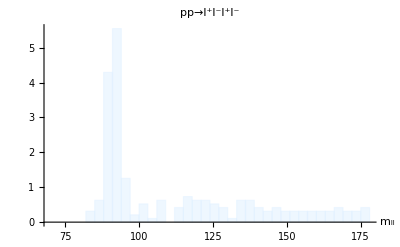

```mathematica
bkgdHist=Histogram[InvMassListRemainbkgd,{70,180,3},#2 (σbkgd*Lumifb)/Nevents&,PlotLabel->"pp→l^+l^-l^+l^-", AxesLabel->{"m_ll"},ChartStyle->Directive[LightBlue,Opacity[0.5]]]
```

```mathematica
InvMassListRemainsig=Flatten[InvMass/@sigcutevents];
```

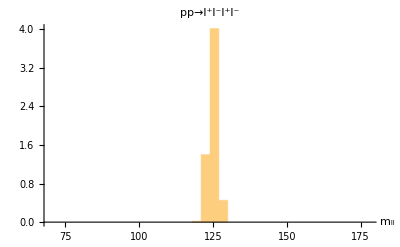

```mathematica
sigHist=Histogram[InvMassListRemainsig,{70,180,3},#2 (σsig*Lumifb)/Nevents&,PlotLabel->"pp→l^+l^-l^+l^-", AxesLabel->{"m_ll"}]
```

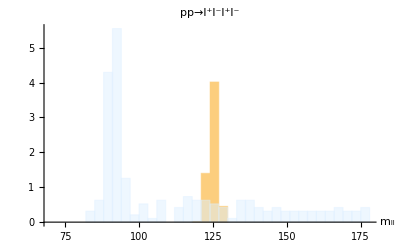

```mathematica
Show[sigHist,bkgdHist]
```

Question 23: How does this plot compare to Fig. 4 of the CMS publication? (2/2)
Answer: Their shapes are very similar. The peaks occur in the same place for both of them. Also, the events don’t die off as much as they used to. They stay consistent with Fig. 4 as we get to 180. However, The signal peak is taller in my histogram compared to the background peak.

The signal events are localized within this distribution. Let’s focus on the mass range that CMS identified, between 120 and 130 GeV. 
To do this we add one final cut on invariant mass.
Directive 15: Rerun the cuts on the smeared signal and background events, then determine the significance of the search at a physical collider. (10/10)

```mathematica
cutnames ={
"No Cuts",(*1*)
"Trigger: 4 Lepton",(*2*)
"      μμμμ",(*3*)
"      eeee",(*4*)
"      eeμμ",(*5*)
"Cut: Z mass [40,120]",(*6*)
"Cut: Z^* mass [12,120] ",(*7*)
"Cut: Inv mass [120,130]" (*8*)
};
```

```mathematica
ApplyCuts[eventlist_]:=Module[{currentevent,trigger,mZ,electronEvent,ePlusList,eMinusList,Zfromee,muonEvent,muPlusList,muMinusList,Zfromμμ,mZlist,survivingevents,cutcounter,passcut},

mZ=91.2;


cutcounter=Table[0,{Length[cutnames]}];
survivingevents={};

(*run this each time we pass a cut*)
passcut[cutindex_]:=Module[{},
(*increment cut counter*)
cutcounter[[cutindex]]++;
];

For[i=1,i<(Length[eventlist]+1),i++,

(*Passcut after setting the variables*)
passcut[1];
trigger=0;

currentevent=eventlist[[i]];

electronEvent=GetParticles[currentevent,{PIDeminus,PIDeplus}];
(*Keep only electrons with |rapidity|≤ 2.5 and Subscript[p, T]≥ 7 GeV*)
electronEvent=Select[electronEvent,((ptOf[#]≥7)&&(Abs[etaOf[#]]<2.5))&];

muonEvent=GetParticles[currentevent,{PIDmuminus,PIDmuplus}];
(*Keep only muons with with |η|≤ 2.4 and Subscript[p, T]≥ 5 GeV*)
muonEvent=Select[muonEvent,((ptOf[#]≥5)&&(Abs[etaOf[#]]<2.4))&];

If[Length[electronEvent]+Length[muonEvent]==4,
passcut[2];

(*Four muon case*)
If[Length[muonEvent]==4,
passcut[3];

muPlusList=GetParticles[currentevent,{PIDmuplus}];
muMinusList=GetParticles[currentevent,{PIDmuminus}];

Zfromμμ={{InvMass[muPlusList[[1]],muMinusList[[1]]],InvMass[muPlusList[[1]],muMinusList[[2]]]},{InvMass[muPlusList[[2]],muMinusList[[1]]],InvMass[muPlusList[[2]],muMinusList[[2]]]}};

(*Within each possibility, put the Z which is closest to on shell first in the sublist*)
Zfromμμ=Sort[#,Abs[#1[[1]] - mZ]<Abs[#2[[1]] - mZ]&] &/@Zfromμμ;
(*Sort the sublists such that the first one has the most on shell Z*)
Zfromμμ=Sort[Zfromμμ,Abs[#1[[1,1]] - mZ]<Abs[#2[[1,1]] - mZ]&];

mZlist=Zfromμμ[[1]];

];

(* Four electron case *)
If[Length[electronEvent]==4,
passcut[4];

ePlusList=GetParticles[currentevent,{PIDeplus}];
eMinusList=GetParticles[currentevent,{PIDeminus}];

Zfromee={{InvMass[ePlusList[[1]],eMinusList[[1]]],InvMass[ePlusList[[1]],eMinusList[[2]]]},{InvMass[ePlusList[[2]],eMinusList[[1]]],InvMass[ePlusList[[2]],eMinusList[[2]]]}};

(*Within each possibility, put the Z which is closest to on shell first in the sublist*)
Zfromee=Sort[#,Abs[#1[[1]] - mZ]<Abs[#2[[1]] - mZ]&] &/@Zfromee;
(*Sort the sublists such that the first one has the most on shell Z*)
Zfromee=Sort[Zfromee,Abs[#1[[1,1]] - mZ]<Abs[#2[[1,1]] - mZ]&];

mZlist=Zfromee[[1]];

];

(* 2 muon 2 electron case *)
If[(Length[electronEvent]==2)&&(Length[muonEvent]==2),
passcut[5];

mZlist={InvMass[electronEvent],InvMass[muonEvent]};
mZlist=Sort[mZlist,Abs[#1 - mZ]<Abs[#2 - mZ]&];

];

If[40<mZlist[[1]]<120,
passcut[6];

If[12<mZlist[[2]]<120,
passcut[7];
If[120<InvMass[currentevent]<130,
passcut[8];
AppendTo[survivingevents,currentevent];
];

];

];

];

];

{cutcounter, survivingevents}

];
```

```mathematica
{bkgdcutcounter,bkgdcutevents}=ApplyCuts[smearBkgdo];
```

```mathematica
{sigcutcounter,sigcutevents}=ApplyCuts[smearSigo];
```

```mathematica
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdcutcounter,"Background"],Prepend[sigcutcounter,"Signal"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | Background | Signal
No Cuts | 10000 | 10000
Trigger: 4 Lepton | 1325 | 4980
      μμμμ | 437 | 1394
      eeee | 245 | 1209
      eeμμ | 643 | 2377
Cut: Z mass [40,120] | 572 | 2344
Cut: Z^* mass [12,120]  | 219 | 2132
Cut: Inv mass [120,130] | 17 | 2132

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgd*Lumifb)];
{sigExpCutcounterErr,sigExpCutcounter}=MCtoExpCutlist[sigcutcounter,(σsig*Lumifb)];
sigoverbkgd=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/bkgdExpCutcounter[[i]]],{i,Length[sigExpCutcounter]}];
significance=Table[If[bkgdExpCutcounter[[i]]==0,∞,sigExpCutcounter[[i]]/(√bkgdExpCutcounter[[i]])],{i,Length[sigExpCutcounter]}];
```

```mathematica
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdExpCutcounterErr,"N_bkgd^Exp"],Prepend[sigExpCutcounterErr,"N_sig^Exp"],Prepend[sigoverbkgd,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 1046.24_-5.02195^4.91733 | 27.6224_-0.132588^0.129825 | 0.0264016 | 0.853976
Trigger: 4 Lepton | 138.627_-1.77861^1.77861 | 13.756_-0.0939162^0.0911539 | 0.0992301 | 1.16833
      μμμμ | 45.7207_-1.04624^1.04624 | 3.85056_-0.0497203^0.0497203 | 0.0842193 | 0.569466
      eeee | 25.6329_-0.836992^0.732368 | 3.33955_-0.0469581^0.0441958 | 0.130284 | 0.659613
      eeμμ | 67.2732_-1.25549^1.25549 | 6.56584_-0.0635315^0.0635315 | 0.0975997 | 0.800515
Cut: Z mass [40,120] | 59.8449_-1.15086^1.15086 | 6.47469_-0.0635315^0.0635315 | 0.108191 | 0.836961
Cut: Z^* mass [12,120]  | 22.9127_-0.732368^0.732368 | 5.8891_-0.0607693^0.0607693 | 0.257024 | 1.2303
Cut: Inv mass [120,130] | 1.77861_-0.209248^0.209248 | 5.8891_-0.0607693^0.0607693 | 3.31107 | 4.41579

Question 24: What is the discovery significance for this narrower invariant mass range? (2/2)
Answer: It means that we have a really good idea of what the mass of the Higgs boson must be.
Question 25: How does this expected significance compare to what is recorded in the final paragraph of Sec. 5.2 of the CMS paper? (2/2)
Answer: It is very similar. We have a strong statistical presence from 120 < m_H<130 GeV and the sig is at about 3.3, which is close to the paper’s 3.2.
Question 26: You’ve “discovered” the Higgs. What are you going to do now? (2/2)
Answer: I’m going to Disneyland!